# Physics through Computational Thinking Week-8: Random Walks

In this tutorial, we discuss random walks using Mathematica. A random walk is  a stochastic/random process -- describes a path consisting of successive random steps.

## 1. 1D Random Walk

Monte Carlo simulations uses random numbers.

Generating Random Numbers

```mathematica
RandomReal[{-1,1}]
```

0.683259

```mathematica
RandomReal[{-1,1},10]
```

{0.193618,-0.156796,-0.084474,-0.118444,-0.895528,-0.210698,-0.596088,-0.161012,-0.254404,-0.674694}

Generating Random Choice

At each step we move +1 or -1 with equal probability.

```mathematica
RandomChoice[{-1,1}]
```

-1

```mathematica
RandomChoice[{-1,1},5]
```

{1,1,-1,-1,-1}

```mathematica
RandomChoice[{0.5,0.5}->{-1,1},15]
```

{-1,1,-1,1,1,1,1,-1,-1,1,-1,-1,1,-1,-1}

```mathematica
randomWalk[n_]:=Accumulate[Prepend[RandomChoice[{-1,1},n],0]] (*simple random walk*)
```

Prepend[..,0]-> preparing the data for a fixed start point. Starting point here is the origin.

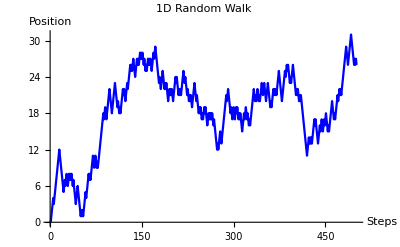

```mathematica
ListLinePlot[randomWalk[500],PlotStyle->Blue,AxesLabel->{"Steps","Position"},PlotLabel->"1D Random Walk"]
```

Average position of the walker stays at the origin (both +1 and -1 step have equal probability), even after many steps.

Since all the steps are independent, the variance is n and the standard deviation σ=√n.

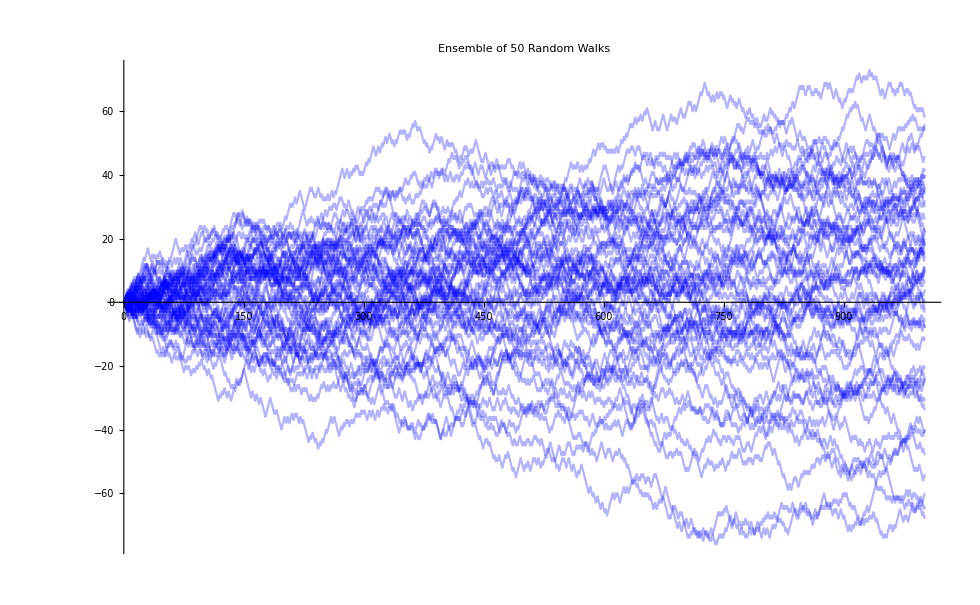

```mathematica
paths=Table[randomWalk[1000],{50}]; (*Visualize 50 paths simultaneously*)
ListLinePlot[paths,PlotStyle->Directive[Opacity[0.3],Blue],PlotLabel->"Ensemble of 50 Random Walks"]
```

```mathematica
nsteps=1000;
finalpos=Table[Total[RandomChoice[{-1,1},nsteps]],{50}];(*final position for 50 paths*)
```

Total[]-> gives the final position after n steps.

```mathematica
Mean[finalpos]//N
```

0.84

```mathematica
StandardDeviation[finalpos]//N
```

33.7

Now compute how the spread grows with time.

```mathematica
rms=Table[Sqrt[Mean[Take[randomWalk[nsteps],t]^2]],{t,10,nsteps,10}];
```

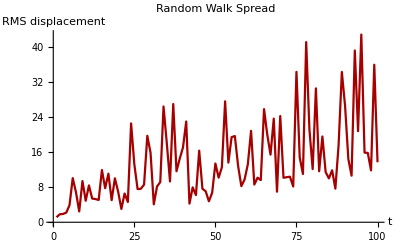

```mathematica
ListLinePlot[rms,AxesLabel->{"t","RMS displacement"},PlotLabel->"Random Walk Spread"]
```

Curve growing like √t.

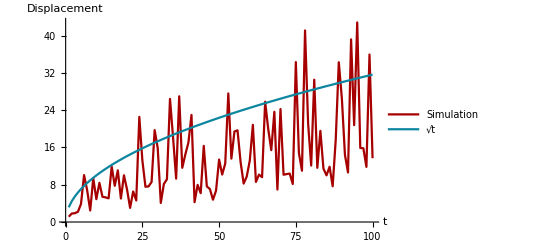

```mathematica
ListLinePlot[{rms,Table[Sqrt[t],{t,10,nsteps,10}]},PlotLegends->{"Simulation","√t"},AxesLabel->{"t","Displacement"}]
```

This is the RMS of one path, it won't consistently show the √t scaling because a single walker might just happen to stay near the origin or drift far away by pure luck. To see the √t behavior, you need to average over many different walkers, i.e., the RMS of all their positions at each time step t.

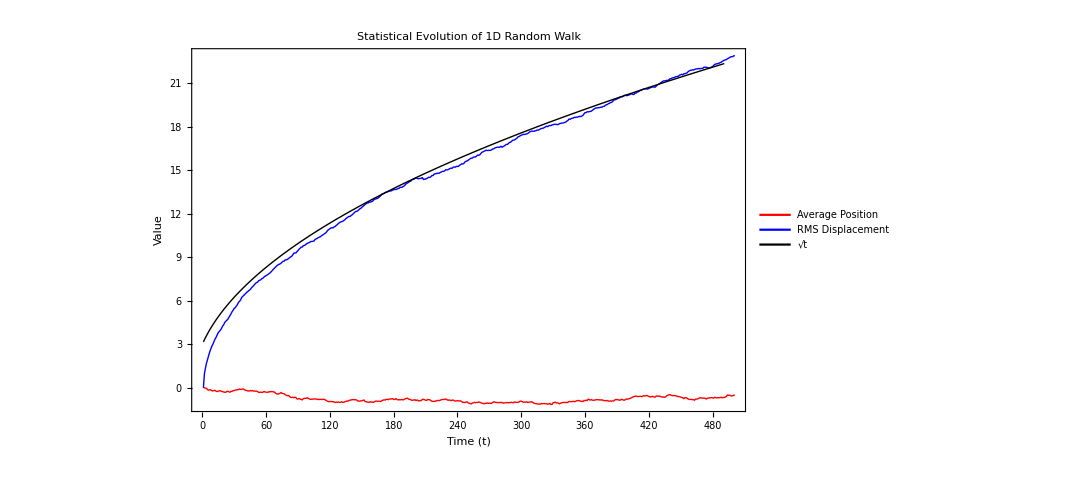

```mathematica
nsteps=500;
nwalk=1000;

ensemble=Table[randomWalk[nsteps],{nwalk}]; (*Generate an ensemble:rows are walkers,columns are time steps*)

timeSlices=Transpose[ensemble]; (*Transpose to look at all walkers at each specific time t*)

avg=Mean/@timeSlices;
rms=Sqrt[Mean[#^2]&/@timeSlices]; (*Calculate Average and RMS for each time point*)

(*Visualize both*)
ListLinePlot[
{avg,rms,Table[Sqrt[t],{t,10,nsteps,1}]},
PlotLegends->{"Average Position","RMS Displacement","√t"},
PlotStyle->{Directive[Thick,Red],Directive[Thick,Blue],Directive[Thick,Black]},
Frame->True,FrameLabel->{"Time (t)","Value"},
PlotLabel->"Statistical Evolution of 1D Random Walk"]
```

```mathematica
N[Sqrt[500]]
```

22.3607

```mathematica
Manipulate[ListLinePlot[randomWalk[nsteps],PlotRange->All,AxesLabel->{"step","position"}],{nsteps,10,2000}]
```

ListLinePlot::lpn: randomWalk[1408.] is not a list of numbers or pairs of numbers.

```mathematica
Manipulate[Column[
{Histogram[Table[Last[Accumulate[RandomChoice[{-1,1},n]]],{5000}],{-n,n,2},"Probability",PlotRange->{{-100,100},{0,0.15}},
PlotLabel->"Distribution of Endpoints at n = "<>ToString[n],
ImageSize->Large],Text[Style["Theoretical Standard Deviation (√n): "<>ToString[N[Sqrt[n]]],14,Bold]]}],
{{n,100,"nsteps"},10,1000,10}]
```

Quadruple the number of steps (n), the "width" of the distribution only doubles (~√n=2).

How does the walk behave as N-> inf?

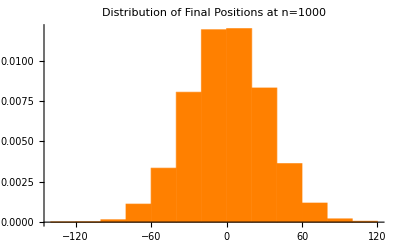

```mathematica
endpoints=Table[Last[randomWalk[1000]],{10000}]; (*Histogram of 10,000 walk endpoints*)
hist=Histogram[endpoints,Automatic,"PDF",
PlotLabel->"Distribution of Final Positions at n=1000",
ChartStyle->Orange]
```

In practice, we use the “PDF” (Probability Density Function) such that the total area of the bars sums to 1.

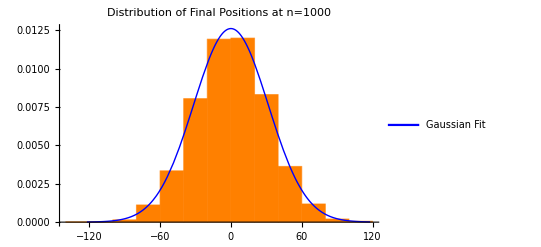

```mathematica
(* Theoretical Gaussian curve with Mean=0 and StdDev=√n *)
gaussCurve=Plot[PDF[NormalDistribution[0,Sqrt[1000]],x],{x,Min[endpoints],Max[endpoints]},PlotStyle->{Thick,Blue},PlotLegends->{"Gaussian Fit"}];

Show[hist,gaussCurve]
```

This is known as Central Limit Theorem (CLT) 
Now, we adding a drift (bias) -- this represents an external force (for example, an electric field acting on a charged particle).

If  is the probability of moving  and  is the probability of moving :

```mathematica
Manipulate[
Module[{nsteps=200,nwalk=50,fairPaths,biasedPaths,fairAvg,biasedAvg},

(*Generate Fair Walk (p=0.5)*)fairPaths=Table[Accumulate[Prepend[RandomChoice[{0.5,0.5}->{-1,1},nsteps],0]],{nwalk}]; 
fairAvg=Mean[fairPaths];

(*Generate Biased Walk (p=prob)*)biasedPaths=Table[Accumulate[Prepend[RandomChoice[{1-prob,prob}->{-1,1},nsteps],0]],{nwalk}];
biasedAvg=Mean[biasedPaths];

GraphicsGrid[{
{ListLinePlot[fairPaths,PlotStyle->Directive[Opacity[0.2],Blue],Epilog->{Red,Thick,Line[Thread[{Range[0,nsteps],fairAvg}]]},
PlotLabel->"Fair Walk (p=0.5)",
Frame->True,
ImageSize->Medium],
ListLinePlot[biasedPaths,PlotStyle->Directive[Opacity[0.2],Green],Epilog->{Red,Thick,Line[Thread[{Range[0,nsteps],biasedAvg}]]},PlotLabel->"Biased Walk (p="<>ToString[prob]<>")",
Frame->True,
ImageSize->Medium]}
}]
],
{{prob,0.6,"Right-move Probability (p)"},0.1,0.9,0.05,Appearance->"Labeled"}]
```

Thread[]-> combines them element-by-element. For example,

```mathematica
x={0,1,2,3,4,5}; (* x={x1,x2,x3,...} *)
y={0,0.1,0.3,0.6,1.0,1.5}; (* y={y1,y2,y3,...} *)
Thread[{x,y}](* return {{x1,y1},{x2,y2},{x3,y3},...} *)
```

{{0,0},{1,0.1},{2,0.3},{3,0.6},{4,1.},{5,1.5}}

Using this we plot the average distance over all the paths at a given time step.

```mathematica
Range[0,5] (*creates x coordiante uniformly from 0 to 5*)
```

{0,1,2,3,4,5}

```mathematica
Range[0,1.5,0.3]
```

{0.,0.3,0.6,0.9,1.2,1.5}

Problem-1: A random walker walking along the x-axis, has a slight bias to move towards the right. At each point, he moves to the right with probability  . If he starts at the origin and takes 100 steps, what is the probability of finding him at x=50?

Let  be the number of steps to the right () and  be the number of steps to the left ().

Total steps, n=n_R+n_L=100.

Net displacement, d=n_R-n_L=50.

```mathematica
nsteps=100;
p=0.65;
nR=75;

prob=Binomial[nsteps,nR]*p^nR*(1-p)^(nsteps-nR)
```

0.00901465

Problem-2: Calculate the ratio of Stirling’s approximation to the exact factorial, , for . Then, determine the minimum integer  required for this ratio to be within  of unity (i.e., the ratio must be )

```mathematica
n=10;
stirling=Sqrt[2*Pi*n]*(n/Exp[1])^n;
actual=Factorial[10];

ratio=N[stirling/actual,20]
```

0.99170403955606148634

```mathematica
Manipulate[
Module[{exact,approx,error,ratio},
exact=Factorial[n];
approx=Sqrt[2*Pi*n]*(n/E)^n;
error=Abs[exact-approx]/exact*100;
ratio=approx/exact;

Column[{
Grid[{
{Style["n",Bold],Style["Exact Factorial",Bold],Style["Stirling Approx",Bold],Style["Ratio",Bold]},
{n,ScientificForm[N[exact,5]],ScientificForm[N[approx,5]],N[ratio,{6,5}]}
},
Frame->All,
Spacings->{2,1},
Background->{None,{Lighter[Gray,0.9]}}

],Spacer[10],

Plot[Sqrt[2*Pi*x]*(x/E)^x/Gamma[x+1],{x,1,100},
PlotRange->{0.9,1.05},
Frame->True,GridLines->{{},{1}},
PlotStyle->Darker[Green],
ImageSize->400,
Epilog->{Red,PointSize[Medium],Point[{n,ratio}]}]
},
Alignment->Center]
],{{n,10,"Value of n"},1,100,1,Appearance->"Labeled"}]
```

Note that the green line stays below 1.0. This tells us Stirling's approximation always slightly underestimates the factorial.

Problem-3:

For an unbiased random walk, the mean square displacement scales linearly with the number of steps: . We now, investigate the scaling behavior of the fourth moment, .

```mathematica
Quit[]
```

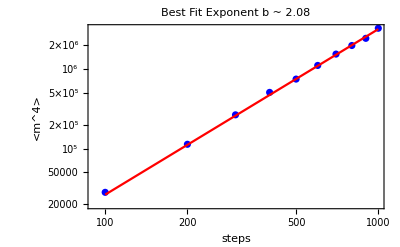

```mathematica
steps=Range[100,1000,100];
nwalk=5000(*Large ensemble*);

m4Data=Table[endpoints=Table[Last[Accumulate[RandomChoice[{-1,1},n]]],{nwalk}];
{n,Mean[endpoints^4]},{n,steps}];

nlm=NonlinearModelFit[m4Data,a*x^b,{a,b},x]; (*power-law fit*)


resultB=b/. nlm["BestFitParameters"];

Show[
ListLogLogPlot[m4Data,PlotStyle->Blue],
LogLogPlot[nlm[x],{x,100,1000},PlotStyle->Red],PlotLabel->Row[{"Best Fit Exponent b ~ ",NumberForm[resultB,{3,2}]}],
Frame->True,FrameLabel->{"steps","<m^4>"}]
```

Generate an ensemble of unbiased random walks for a range of steps N∈{50,100,200,500,1000}. For each , calculate the ratio: .

Using Mathematica, plot this ratio  against . What value does the ratio approach as  becomes large, and what does this tell us about the shape of the random walk's distribution?

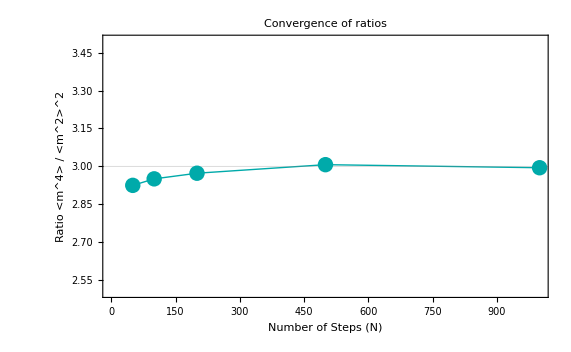

```mathematica
nList={50,100,200,500,1000}; (*create a list for N*)
nwalk=10000;(*Large ensemble*)

ratio=Table[endpoints=Table[Last[Accumulate[RandomChoice[{-1,1},n]]],{nwalk}];
m2=Mean[endpoints^2];
m4=Mean[endpoints^4];
{n,m4/(m2^2)},{n,nList}]; (*Calculate Ratio for each N*)


ListLinePlot[ratio,Mesh->All,PlotRange->{2.5,3.5},GridLines->{{},{3}},
PlotStyle->{Thick,Darker[Cyan]},Frame->True,FrameLabel->{"Number of Steps (N)","Ratio <m^4> / <m^2>^2"},PlotLabel->"Convergence of ratios"]
```

This ratio converge to 3. This is the definition of the Kurtosis of a normal distribution.

As  increases, the Central Limit Theorem (CLT) ensures the discrete binomial distribution of the random walk transforms into a Gaussian Distribution.

For a Gaussian distribution (which the random walk approaches via the CLT), the moments are related. If , then:

κ==⟨m^4⟩/(⟨m^2⟩^2)=3.0

Next, we discuss the kurtosis of a biased walk , which helps us to understand how the symmetry of a distribution (or lack thereof) affects higher-order moments.

In the unbiased case (), we saw the ratio  converge to . Now, we introduce a strong bias (e.g., ).

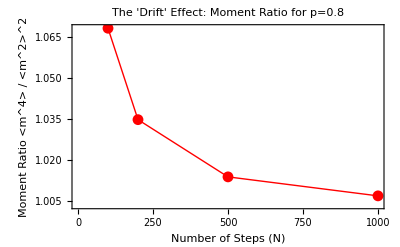

```mathematica
nList={100,200,500,1000};
nwalk=10000;
p=0.8;(*Strong Bias*)

ratio=Table[endpoints=Table[Last[Accumulate[RandomChoice[{1-p,p}->{-1,1},n]]],{nwalk}];
m2=Mean[endpoints^2];
m4=Mean[endpoints^4];
{n,m4/(m2^2)},{n,nList}];(*Moment Ratio for Biased Walk*)


ListLinePlot[ratio,Mesh->All,PlotStyle->{Thick,Red},
Frame->True,
FrameLabel->{"Number of Steps (N)","Moment Ratio <m^4> / <m^2>^2"},PlotLabel->"The 'Drift' Effect: Moment Ratio for p=0.8"]
```

We see that the ratio converges to ~1, not 3.

This is because, in a biased walk, the displacement is dominated by the drift ().

To get the value of 3, we must use Central Moments:

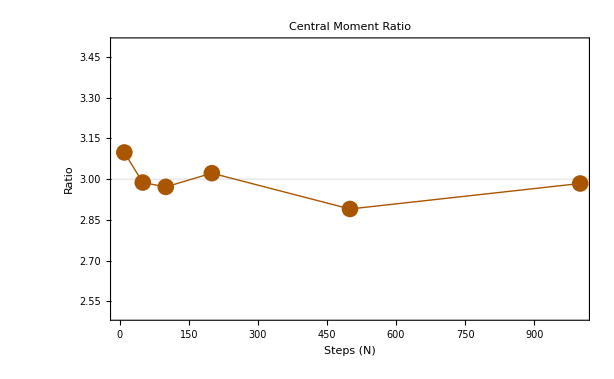

```mathematica
nList={10,50,100,200,500,1000};
nwalk=10000;
p=0.8;

ratio=Table[endpoints=Table[Last[Accumulate[RandomChoice[{1-p,p}->{-1,1},n]]],{nwalk}];
cm2=CentralMoment[endpoints,2];
cm4=CentralMoment[endpoints,4];
{n,cm4/(cm2^2)},{n,nList}]; (*calculate central moment ratio*)


ListLinePlot[ratio,Mesh->All,PlotRange->{2.5,3.5},GridLines->{{},{3}},PlotStyle->{Thick,Darker[Orange]},Frame->True,FrameLabel->{"Steps (N)","Ratio"},PlotLabel->"Central Moment Ratio"]
```

The central moment only measures the “Spread”.

Let’s given the probability density function (PDF) for a single step  is: 
=> This is a standard Exponential Distribution with rate parameter .

The "spread" requested is the Standard Deviation of the total distance :  .

Numerical Spread: 15.7919

Theoretical Spread (√N/2): 15.8114

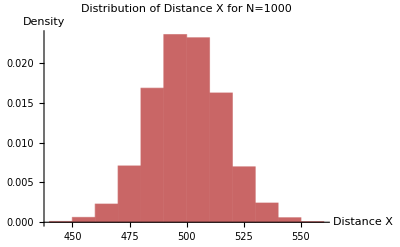

```mathematica
n=1000;
lambda=2;

dist=ExponentialDistribution[lambda]; (*exponential distribution*)

(*Simulate 10,000 walkers taking N steps each*)
nwalk=10000;
samples=Table[Total[RandomVariate[dist,n]],{nwalk}];

(*Calculate numerical Spread*)
numericalSpread=StandardDeviation[samples]//N;
theoreticalSpread=Sqrt[n]/lambda//N;

Print["Numerical Spread: ",numericalSpread];
Print["Theoretical Spread (√N/2): ",theoreticalSpread];

(*Visualization*)
Histogram[samples,Automatic,"PDF",
PlotLabel->"Distribution of Distance X for N=1000",
AxesLabel->{"Distance X","Density"},Epilog->{Red,Thick,Dashed,Line[{{theoreticalSpread,0},{theoreticalSpread,0.05}}]}]
```

```mathematica
hist=Histogram[samples,Automatic,"PDF",PlotLabel->"CLT: Sum of Exponential Steps (N=1000)"];
```

```mathematica
gauss=Plot[PDF[NormalDistribution[n/2,√n/2],x],{x,n/2-4 √n/2,n/2+4 √n/2},PlotStyle->{Thick,Blue},PlotLegends->{"Gaussian"}];
```

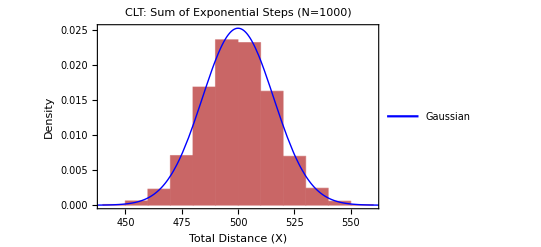

```mathematica
Show[hist,gauss,Frame->True,FrameLabel->{"Total Distance (X)","Density"}]
```

Even though the walker only moves right (a completely biased walk in terms of direction), there is still a "spread" in their final position. This is because the length of the steps is uncertain.

This is a fundamental result of the Central Limit Theorem: the sum of  exponential variables will eventually look like a Gaussian centered at  with a width of .